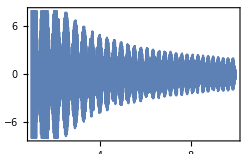

-Graphics-

```mathematica
baseFreq=440;
Plot[(10/t)(Cos[baseFreq*2Pi t]+Cos[(baseFreq+√t)*2Pi t]),{t,1,10},Frame->True]
Play[(10/t)(Cos[baseFreq*2Pi t]+Cos[(baseFreq+√t)*2Pi t]),{t,1,10}]
```

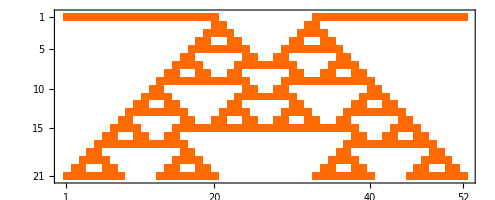

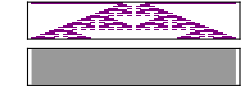

```mathematica
MatrixPlot@CellularAutomaton[90,{{1,0,0,0,0,0,0,0,0,0,0,0,0,1},{1}},20]
Sound[SoundNote[DeleteCases[4 Range[21]Reverse[#],0]-24,.1]&/@Transpose[CellularAutomaton[90,{{1,0,0,0,0,0,1},{1}},20]]]
```

```mathematica
SoundNote[DeleteCases[3 Range[21]Reverse[#],""]-24,.1]&/@Transpose[CellularAutomaton[90,{{1,0,0,0,0,0,1},{1,0}},20]]
```

```mathematica
CellularAutomaton[90,{{1,0,0,0,0,0,1},{1}},20]
```

```mathematica
DeleteCases[3 Range[21]Reverse[#],0]&/@Transpose[CellularAutomaton[90,{{1,0,0,0,0,0,1},{1}},20]]
```

{{3,63},{3,6,63},{3,6,9,63},{3,9,12,63},{3,9,12,15,63},{6,9,15,18,63},{15,18,21,63},{6,9,15,21,24,63},{3,9,12,15,21,24,27,63},{3,9,12,18,21,27,30,63},{3,6,9,27,30,33,63},{3,6,18,21,27,33,36,63},{3,21,24,27,33,36,39,63},{18,21,24,30,33,39,42,63},{39,42,45,63},{18,21,24,30,33,39,45,48,63},{21,24,27,33,36,39,45,48,51,63},{18,21,27,33,36,42,45,51,54,63},{27,30,33,51,54,57,63},{18,21,27,30,42,45,51,57,60,63},{21,24,27,45,48,51,57,60},{18,21,24,42,45,48,54,57},{},{18,21,24,42,45,48,54,57},{21,24,27,45,48,51,57,60},{18,21,27,30,42,45,51,57,60,63},{27,30,33,51,54,57,63},{18,21,27,33,36,42,45,51,54,63},{21,24,27,33,36,39,45,48,51,63},{18,21,24,30,33,39,45,48,63},{39,42,45,63},{18,21,24,30,33,39,42,63},{3,21,24,27,33,36,39,63},{3,6,18,21,27,33,36,63},{3,6,9,27,30,33,63},{3,9,12,18,21,27,30,63},{3,9,12,15,21,24,27,63},{6,9,15,21,24,63},{15,18,21,63},{6,9,15,18,63},{3,9,12,15,63},{3,9,12,63},{3,6,9,63},{3,6,63},{3,63}}

```mathematica
3 Range[21]
```

{3,6,9,12,15,18,21,24,27,30,33,36,39,42,45,48,51,54,57,60,63}